# 2D Overlap Integrals from Rotated Model Potentials Zachary K. Goldsmith

## Constants

### Unit conversions

```mathematica
bohr2a=0.529177`30;
a2bohr=1/bohr2a;
au2kcal=627.5095`30;
kcal2au=1/au2kcal;
ev2cm=8065.54477`30;
cm2ev = 1/ev2cm ;
au2ev=27.2113`30;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
au2ps=2.4189`30 10^-5;
```

### Universal constants

```mathematica
ℏ=1; 
hbarps=(0.047685388`30)/(au2kcal π);
Dalton=1822.8880`30;
μH=1836.1526675`30;
μD=3670.4829550`30;
kb=3.16683`30 10^-6;
```

### System constants

```mathematica
xAuH=1.0`30;
```

```mathematica
xAH=1.0`30;
```

```mathematica
xx[R_,θ_]:=SetAccuracy[R-xAH Cos[θ],30];
```

```mathematica
yy[θ_]:=SetAccuracy[xAH Sin[θ],30];
```

### Accuracy settings

```mathematica
AccN=100;
```

## 1D and 2D potentials

#### 1D Morse potential for stretching

```mathematica
UMorse[x_,x0_,DE_,β_]:=DE(1-Exp[-β (x-x0)])^2;
```

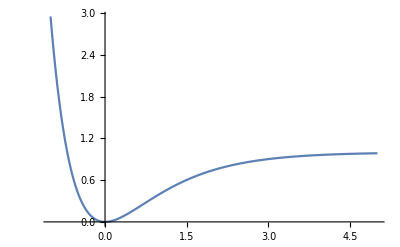

```mathematica
Plot[UMorse[x,0,1,1],{x,-1,5},PlotRange->All]
```

#### 1D Potentials for bending

```mathematica
UMorseSym[y_,y0_,DE_,β_]:=DE(1-Exp[-β Abs[y-y0]])^2; (*Morse w/ abs value, dissociative bending potential*)
```

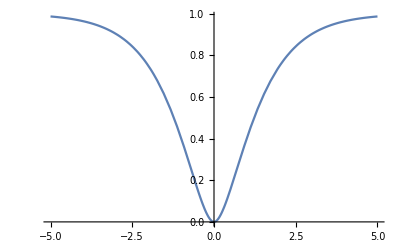

```mathematica
Plot[UMorseSym[y,0,1,1],{y,-5,5},PlotRange->All]
```

```mathematica
UGauss[y_,y0_,DE_,Α_]:=DE(1-Exp[-Α (y-y0)^2 ]) (*Upside-down Gaussian potential*)
```

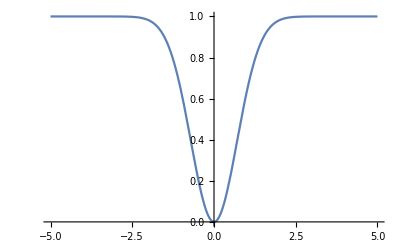

```mathematica
Plot[UGauss[y,0,1,1],{y,-5 ,5},PlotRange->All]
```

```mathematica
UTanh[y_,y0_,DE_,Α_]:=DE Tanh[Α (y-y0)]^2 (*Hyperbolic tangent potential*)
```

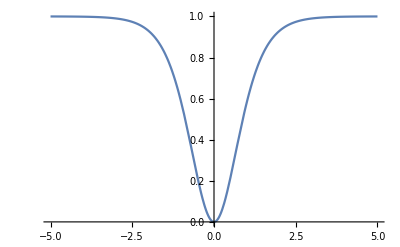

```mathematica
Plot[UTanh[y,0,1,1],{y,-5 ,5},PlotRange->All]
```

```mathematica
UHarm[y_,y0_,k_]:=0.5 k (y-y0)^2 (*Harmonic potential, non-dissociative*)
```

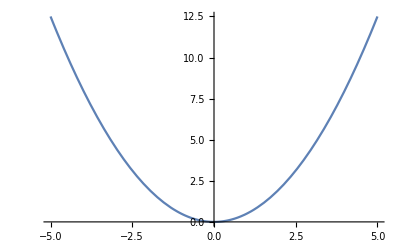

```mathematica
Plot[UHarm[y,0,1],{y,-5,5},PlotRange->All]
```

#### Building the 2D potential

```mathematica
UHarm2D[x_,x0_,y_,y0_,kx_,ky_]:=UHarm[x,x0,kx]+UHarm[y,y0,ky]
```

```mathematica
Plot3D[UHarm2D[x,0,y,0,2,1],{x,-1,1},{y,-1,1},PlotRange->All,Boxed->False,ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
UMorseHarm2D[x_,x0_,DE_,β_,y_,y0_,ky_]:=UMorse[x,x0,DE,β]+UHarm[y,y0,ky]
```

```mathematica
Plot3D[UMorseHarm2D[x,0,1,1.1,y,0,1],{x,-2,1},{y,-10,10},PlotRange->All,Boxed->False,ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
Plot3D[UMorse[x,0,1,1]+UMorseSym[y,0,1,1],{x,-1,3},{y,-2,2},PlotRange->All,Boxed->False,ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
Plot3D[UMorse[x,0,1,1]+UGauss[y,0,1,1],{x,-1,3},{y,-2,2},PlotRange->All,Boxed->False,ColorFunction->"DarkRainbow"]
```

-Graphics3D-

```mathematica
Plot3D[UMorse[x,0,1,1]+UTanh[y,0,1,1],{x,-1,3},{y,-2,2},PlotRange->All,Boxed->False,ColorFunction->"DarkRainbow"]
```

-Graphics3D-

## 2D wavefunction solver for general potentials on a square grid

```mathematica
GenSquareGridSolverN2D[vGrid_,nGrid_,a_,nRoots_,OptionsPattern[{M->1,DiffOrder->4}]]:=Module[{μ,xRange,xyList,T,V,h,en,v,nOrder},
nOrder=OptionValue[DiffOrder];
μ=OptionValue[M];
xRange=Range[1,nGrid];
xyList=Tuples[xRange,2];
T=-
1/(2 μ a^2) Sum[
NDSolve`FiniteDifferenceDerivative[i,{xRange,xRange},"DifferenceOrder"->nOrder]
["DifferentiationMatrix"],
{i,{{2,0},{0,2}}}];
V=DiagonalMatrix[SparseArray[(vGrid⟦##⟧&@@@xyList)]];
h=N[T+V];
en=Reverse@Re@Eigenvalues[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
v=Reverse@Re@Eigenvectors[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
{en,Table[Partition[v⟦i⟧,nGrid],{i,1,Length[v]}]}
];
```

Check:

```mathematica
nX=100;
xmax=6;
a=xmax/nX;
```

```mathematica
vGridharm2D=Table[UHarm2D[x,0,y,0,1,1],{x,-4,4,a},{y,-4,4,a}];
```

```mathematica
solharm2D=GenSquareGridSolverN2D[vGridharm2D,2nX+1,a,10,M->1.0,DiffOrder->3];
```

```mathematica
solharm2D⟦1⟧
```

{0.999999,1.99999,1.99999,2.99997,2.99997,2.99999,3.99997,3.99997,4.00012,4.00012}

```mathematica
ListPlot3D[solharm2D⟦2,4⟧,PlotRange->All,Boxed->False,Axes->False,ColorFunction->"DarkRainbow"]
```

-Graphics3D-

## Rotation of potentials by angle θ

```mathematica
UHarm2Drot[x_,x0_,y_,y0_,θ_,kx_,ky_]:=UHarm2D[x Cos[θ]-y Sin[θ],x0 Cos[θ]-y0 Sin[θ],x Sin[θ]+y Cos[θ],x0 Sin[θ]+y0 Cos[θ],kx,ky];
```

```mathematica
Plot3D[UHarm2Drot[x,0,y,0,0.,2,1],{x,-1,1},{y,-1,1},PlotRange->All,Boxed->False,ColorFunction->"DarkRainbow"]
```

-Graphics3D-

## 2D wavefunctions, energy levels, and overlaps of general rotated potentials at fixed θ

```mathematica
R=Table[i,{i,xAuH+xAH,3,0.5}];
```

```mathematica
θ=π/6;
```

```mathematica
nR=Length[R];
nRoots=6;
```

```mathematica
ClearAll[wfHOx,wfHRed,enHOx,enHRed];
ClearAll[wfDOx,wfDRed,enDOx,enDRed];
```

```mathematica
Array[wfHOx,{nR,nRoots}];
Array[wfHRed,{nR,nRoots}];
Array[enHOx,nR];
Array[enHRed,nR];
```

```mathematica
Array[wfDOx,{nR,nRoots}];
Array[wfDRed,{nR,nRoots}];
Array[enDOx,nR];
Array[enDRed,nR];
```

```mathematica
Array[SH,nR];
Array[SD,nR];
```

```mathematica
(*Wavefunctions and overlaps as a function of R and θ*)
```

```mathematica
Do[
Block[{xmax,nX,dx,xx,yy,vGridOx,vGridRed,solOx,solRed},
xmax=5;
nX=128;
dx=xmax/nX;
xx=R⟦iR⟧-xAH Cos[θ];
yy=xAH Sin[θ];
vGridOx=Table[UHarm2Drot[x,xx,y,yy,θ,1,1],{x,-3,7,dx},{y,-5,5,dx}];
vGridRed=Table[UHarm2Drot[x,xAuH,y,0,0,1,1],{x,-3,7,dx},{y,-5,5,dx}];
solOx=GenSquareGridSolverN2D[vGridOx,2nX+1,dx,nRoots,M->1.0,DiffOrder->3];
solRed=GenSquareGridSolverN2D[vGridRed,2nX+1,dx,nRoots,M->1.0,DiffOrder->3];
Do[
wfHOx[iR,iRoot]=solOx⟦2,iRoot⟧;
wfHRed[iR,iRoot]=solRed⟦2,iRoot⟧,
{iRoot,1,nRoots}];
enHOx[iR]=solOx⟦1⟧;
enHRed[iR]=solRed⟦1⟧;]
,{iR,1,nR}]
```

```mathematica
(*Compute overlaps*)
```

```mathematica
Do[
SH[iR]=ParallelTable[Flatten[wfHOx[iR,i]]. Flatten[wfHRed[iR,j]],{i,1,nRoots},{j,1,nRoots}];
(*SD[iR]=ParallelTable[Flatten[wfDOx[iR,i]] . Flatten[wfDRed[iR,j]],{i,1,nRoots},{j,1,nRoots}]*)
,{iR,1,nR}]
```

```mathematica
SH[2]⟦1⟧⟦1⟧
```

-0.849607

## 2D wavefunctions, energy levels, and overlaps of general rotated potentials at variable θ

```mathematica
R=Table[i,{i,xAuH+xAH,3,0.5}];
```

```mathematica
θ=Table[i,{i,0,π/6,π/6}];
```

```mathematica
nR=Length[R];
nθ=Length[θ];
nRoots=6;
```

```mathematica
ClearAll[wfHOx,wfHRed,enHOx,enHRed];
ClearAll[wfDOx,wfDRed,enDOx,enDRed];
```

```mathematica
Array[wfHOx,{nR,nθ,nRoots}];
Array[wfHRed,{nR,nθ,nRoots}];
Array[enHOx,nR,nθ];
Array[enHRed,nR,nθ];
```

```mathematica
Array[wfDOx,{nR,nθ,nRoots}];
Array[wfDRed,{nR,nθ,nRoots}];
Array[enDOx,nR,nθ];
Array[enDRed,nR,nθ];
```

```mathematica
Array[SH,{nR,nθ}];
Array[SD,{nR,nθ}];
```

```mathematica
(*Wavefunctions and overlaps as a function of R and θ*)
```

```mathematica
Do[
Block[{xmax,nX,dx,xx,yy,vGridOx,vGridRed,solOx,solRed},
xmax=5;
nX=128;
dx=xmax/nX;
xx=R⟦iR⟧-xAH Cos[θ⟦iθ⟧];
yy=xAH Sin[θ⟦iθ⟧];
vGridOx=Table[UHarm2Drot[x,xx,y,yy,θ⟦iθ⟧,1,1],{x,-3,7,dx},{y,-5,5,dx}];
vGridRed=Table[UHarm2Drot[x,xAuH,y,0,0,1,1],{x,-3,7,dx},{y,-5,5,dx}];
solOx=GenSquareGridSolverN2D[vGridOx,2nX+1,dx,nRoots,M->1.0,DiffOrder->3];
solRed=GenSquareGridSolverN2D[vGridRed,2nX+1,dx,nRoots,M->1.0,DiffOrder->3];
Do[
wfHOx[iR,iθ,iRoot]=solOx⟦2,iRoot⟧;
wfHRed[iR,iθ,iRoot]=solRed⟦2,iRoot⟧,
{iRoot,1,nRoots}];
enHOx[iR,iθ]=solOx⟦1⟧;
enHRed[iR,iθ]=solRed⟦1⟧;]
,{iR,1,nR},{iθ,1,nθ}]
```

```mathematica
(*Compute overlaps*)
```

```mathematica
Do[
SH[iR,iθ]=ParallelTable[Flatten[wfHOx[iR,iθ,i]]. Flatten[wfHRed[iR,iθ,j]],{i,1,nRoots},{j,1,nRoots}];
(*SD[iR]=ParallelTable[Flatten[wfDOx[iR,i]] . Flatten[wfDRed[iR,j]],{i,1,nRoots},{j,1,nRoots}]*)
,{iR,1,nR},{iθ,1,nθ}]
```

```mathematica
SH[2,2]⟦1⟧⟦1⟧
```

-0.849607

## Analytical overlaps from rotated 2D harmonic potentials

```mathematica
ψharm[x_,x0_,m_,ω_,n_]:=SetAccuracy[((m Dalton ω cm2au)/(π ℏ))^(1/4)1/(2^(n/2)√(n!))Exp[-(m Dalton ω cm2au)/(2ℏ) (x-x0)^2]HermiteH[n,(x-x0)√((m Dalton ω cm2au)/ℏ)],AccN];
```

```mathematica
Integrate[ψharm[x,0,1,3000,0]^2,{x,-∞,∞}]
```

1.00000000000000000000000000000000000000005897016123400737380591207217714750071977630260862523651178

```mathematica
ψharm2D[x_,y_,x0_,y0_,m_,ωx_,ωy_,nx_,ny_]:=Chop[ψharm[x,x0,m,ωx,nx]*ψharm[y,y0,m,ωy,ny],1 ×10^-8];
```

```mathematica
(*ψharm2Drot[x_,y_,x0_,y0_,θ_,m_,ωx_,ωy_,nx_,ny_]:=
ψharm[x Cos[θ]-y Sin[θ],x0 Cos[θ]-y0 Sin[θ],m,ωx,nx]*ψharm[y Cos[θ]+x Sin[θ],y0 Cos[θ]+x0 Sin[θ],m,ωy,ny];*)
```

```mathematica
ψharm2Drot[x_,y_,x0_,y0_,θ_,m_,ωx_,ωy_,nx_,ny_]:=Module[{doverlap},
doverlap=ψharm2D[x Cos[θ]-y Sin[θ],x Sin[θ]+y Cos[θ],x0 Cos[θ]-y0 Sin[θ],x0 Sin[θ]+y0 Cos[θ],m,ωx,ωy,nx,ny];
Chop[doverlap]
];
```

```mathematica
NIntegrate[ψharm2Drot[x,y,0,0,0,1,3000,600,0,0]ψharm2Drot[x,y,0,0,0,1,3000,600,1,1],{x,-∞,∞},{y,-∞,∞}]
```

0.

```mathematica
Manipulate[
Plot3D[{
ψharm2Drot[x,y,xAuH,0,0,1,3000,600,mx,my],
ψharm2Drot[x,y,x0,y0,θ,1,3000,600,nx,ny]
},{x,0,4},{y,-2,2},PlotRange->All,Boxed->False,Axes->{True,True,False}],
{mx,0,5,1},{my,0,5,1},{nx,0,5,1},{ny,0,5,1},{x0,2.5,4,0.25},{y0,0,1,0.25},{θ,0,π/2,π/8}]
```

```mathematica
(*Compute overlap integrals of 2D roatated harmonic wavefunctions, fixed "active site"*)
```

```mathematica
S2D[R_,θ_,m_,ωxAu_,ωyAu_,ωxA_,ωyA_,μx_,μy_,νx_,νy_]:=Module[{xx,yy,integrand},
xx=R-xAH Cos[θ];
yy=xAH Sin[θ];
integrand[x_,y_]:=ψharm2Drot[x,y,xAuH,0,0,m,ωxAu,ωyAu,μx,μy]*ψharm2Drot[x,y,xx,yy,θ,m,ωxA,ωyA,νx,νy];
Chop@Integrate[integrand[x,y],{x,-∞,∞},{y,-∞,∞}] 
]
```

```mathematica
S2D[2,0,1,3000,600,3000,600,0,0,0,0]
```

1.00000000000000000000000000000000000000005897016123402485595361439155271184934737016957551695362

```mathematica
(*Compute overlap integrals of 2D roatated harmonic wavefunctions, "active site" always aligned with donor*)
```

```mathematica
S2Dyy[R_,θ_,m_,ωxAu_,ωyAu_,ωxA_,ωyA_,μx_,μy_,νx_,νy_]:=Module[{xx,yy,integrand},
xx=R-xAH Cos[θ];
yy=xAH Sin[θ];
integrand[x_,y_]:=ψharm2Drot[x,y,xAuH,yy,0,m,ωxAu,ωyAu,μx,μy]*ψharm2Drot[x,y,xx,yy,θ,m,ωxA,ωyA,νx,νy];
Chop@Integrate[integrand[x,y],{x,-∞,∞},{y,-∞,∞}] 
]
```

```mathematica
(*Compute overlap integrals of 2D roatated harmonic wavefunctions for a range of active site positions*)
```

```mathematica
S2DyTable[R_,θ_,m_,ωxAu_,ωyAu_,ωxA_,ωyA_,μx_,μy_,νx_,νy_]:=Table[Module[{xx,yy,integrand},
xx=R-xAH Cos[θ];
yy=xAH Sin[θ];
integrand[x_,y_]:=ψharm2Drot[x,y,xAuH,yy+ystep,0,m,ωxAu,ωyAu,μx,μy]*ψharm2Drot[x,y,xx,yy,θ,m,ωxA,ωyA,νx,νy];
Chop@Integrate[integrand[x,y],{x,-∞,∞},{y,-∞,∞}] 
],{ystep,-1,1,0.25}]
```

```mathematica
Manipulate[S2D[R,θ,1,3000,600,3000,600,μx,μy,νx,νy],{R,xAuH+xAH,4,0.25},{θ,0,π/2,π/8},
{μx,0,5,1},{μy,0,5,1},{νx,0,5,1},{νy,0,5,1}]
```

```mathematica
DiscretePlot[{S2D[R,0,1,3000,600,3000,600,0,0,0,0]^2,S2D[R,0,1,3000,600,3000,600,1,0,0,0]^2,S2D[R,0,1,3000,600,3000,600,0,1,0,0]^2,S2D[R,0,1,3000,600,3000,600,0,0,1,0]^2,S2D[R,0,1,3000,600,3000,600,0,0,0,1]^2},{R,xAH+xAuH,3,0.2},PlotRange->All,Joined->True,Filling->None,PlotLegends->Placed[{"(0,0;0,0)","(1,0;0,0)","(0,1;0,0)","(0,0;1,0)","(0,0;0,1)"},{0.8,0.6}],Frame->True,FrameLabel->{"R, Å","S_μ_x^2"}]
```

$Aborted

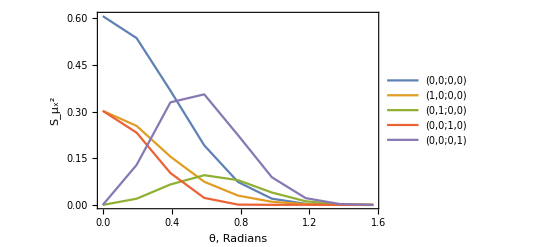

```mathematica
DiscretePlot[{S2D[2.2,θ,1,3000,600,3000,600,0,0,0,0]^2,S2D[2.2,θ,1,3000,600,3000,600,1,0,0,0]^2,S2D[2.2,θ,1,3000,600,3000,600,0,1,0,0]^2,S2D[2.2,θ,1,3000,600,3000,600,0,0,1,0]^2,S2D[2.2,θ,1,3000,600,3000,600,0,0,0,1]^2},{θ,0,π/2,π/16},PlotRange->All,Joined->True,Filling->None,PlotLegends->Placed[{"(0,0;0,0)","(1,0;0,0)","(0,1;0,0)","(0,0;1,0)","(0,0;0,1)"},{0.8,0.6}],Frame->True,FrameLabel->{"θ, Radians","S_μ_x^2"}]
```

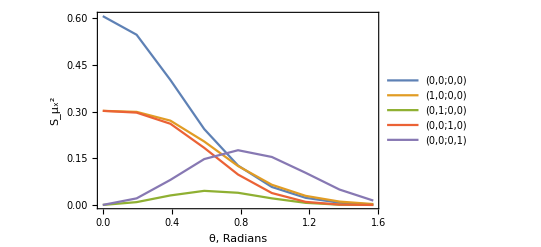

```mathematica
DiscretePlot[{S2Dyy[2.2,θ,1,3000,600,3000,600,0,0,0,0]^2,S2Dyy[2.2,θ,1,3000,600,3000,600,1,0,0,0]^2,S2Dyy[2.2,θ,1,3000,600,3000,600,0,1,0,0]^2,S2Dyy[2.2,θ,1,3000,600,3000,600,0,0,1,0]^2,S2Dyy[2.2,θ,1,3000,600,3000,600,0,0,0,1]^2},{θ,0,π/2,π/16},PlotRange->All,Joined->True,Filling->None,PlotLegends->Placed[{"(0,0;0,0)","(1,0;0,0)","(0,1;0,0)","(0,0;1,0)","(0,0;0,1)"},{0.8,0.6}],Frame->True,FrameLabel->{"θ, Radians","S_μ_x^2"}]
```

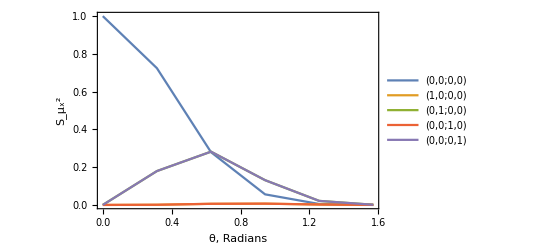

```mathematica
DiscretePlot[{S2D[2,θ,1,3000,600,3000,600,0,0,0,0]^2,S2D[2,θ,1,3000,600,3000,600,1,0,0,0]^2,S2D[2,θ,1,3000,600,3000,600,0,1,0,0]^2,S2D[2,θ,1,3000,600,3000,600,0,0,1,0]^2,S2D[2,θ,1,3000,600,3000,600,0,0,0,1]^2},{θ,0,π/2,π/10},PlotRange->All,Joined->True,Filling->None,PlotLegends->Placed[{"(0,0;0,0)","(1,0;0,0)","(0,1;0,0)","(0,0;1,0)","(0,0;0,1)"},{0.8,0.6}],Frame->True,FrameLabel->{"θ, Radians","S_μ_x^2"}]
```

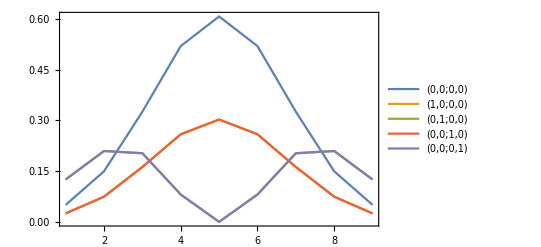

```mathematica
ListLinePlot[{S2DyTable[2.2,0,1,3000,600,3000,600,0,0,0,0]^2,S2DyTable[2.2,0,1,3000,600,3000,600,1,0,0,0]^2,S2DyTable[2.2,0,1,3000,600,3000,600,0,1,0,0]^2,S2DyTable[2.2,0,1,3000,600,3000,600,0,0,1,0]^2,S2DyTable[2.2,0,1,3000,600,3000,600,0,0,0,1]^2},PlotRange->All,Joined->True,Filling->None,PlotLegends->{"(0,0;0,0)","(1,0;0,0)","(0,1;0,0)","(0,0;1,0)","(0,0;0,1)"},Frame->True]
```

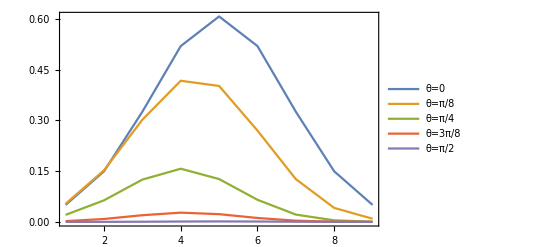

```mathematica
ListLinePlot[{S2DyTable[2.2,0,1,3000,600,3000,600,0,0,0,0]^2,S2DyTable[2.2,π/8,1,3000,600,3000,600,0,0,0,0]^2,S2DyTable[2.2,π/4,1,3000,600,3000,600,0,0,0,0]^2,S2DyTable[2.2,3 π/8,1,3000,600,3000,600,0,0,0,0]^2,S2DyTable[2.2,π/2,1,3000,600,3000,600,0,0,0,0]^2},PlotRange->All,Joined->True,Filling->None,PlotLegends->{"θ=0","θ=π/8","θ=π/4","θ=3π/8","θ=π/2"},Frame->True]
```